```mathematica
ClearAll[phi,possol,velsol,angle,ic];
(*SetDirectory[NotebookDirectory[]];*)
Needs["VariationalMethods`"] (* for function EulerEquations *)
(* N-dulum *)


(* *****  Constants ***** *)
g=9.81; (* gravity *)
m=1;
l=1 ;(* for now all masses=1 and lengths= 1 *)
n=2;(* number of pendula *)
phi0=0.2; (* Starting angle for each *)
tmax=200;(* How long to run the system *)

(* *************  Variable Functions and initial conditions *********************** *)
phis=Table[phi[i][t],{i,1,n}];
velocities=Table[phi[i]'[t],{i,1,n}];
ic[angle_]:=Join[Table[phi[i][0]==angle,{i,1,n}],Table[phi[i]'[0]==0,{i,1,n}]];

(*  *********  Cartesian Coords for each, i, pendulum  **********  *)
x=Table[Sum[l*Sin[phi[j][t]],{j,1,i}],{i,1,n}] ;(* Lists of coords for each pendulum. For now mi=li=1. Otherwise l is multiplied in *)
y=Table[Sum[-l*Cos[phi[j][t]],{j,1,i}],{i,1,n}] ;
r=Table[{x[[i]],y[[i]]},{i,1,n}];
r[[0]]={0,0};

(* ****************  Energies  *********************** *)
(* Potential Energy. mi=li=1, otherwise multiply in these terms *)
pots=Table[(m*g).{0,1}.r[[i]],{i,1,n}];
potential=g*m{0,1}.Sum[r[[i]],{i,1,n}];

(* Kinetic energy *)
kinetic=0.5*Sum[m*(D[r[[i]],t].D[r[[i]],t]),{i,1,n}];


(* Lagrangian *)
L=kinetic-potential; 

motion=EulerEquations[L,phis,t];

 (* solves for given initial conditions and duration *)
possol[initials_,start_,end_]:=
NDSolve[Join[motion,initials],phis,{t,start,end},Method->{"EquationSimplification"->"Residual"}];
velsol[initials_,start_,end_]:=
NDSolve[Join[motion,initials],velocities,{t,start,end},Method->{"EquationSimplification"->"Residual"}];

(* ************** Plots ************* *)
(*Plot[Evaluate[phis/.possol],{t,0,tmax},AxesLabel->{time,position}]
ParametricPlot[Evaluate[{phis/.possol,velocities/.velsol}],{t,0,tmax},PlotRange->All]*)
```

```mathematica
ClearAll[j,k,runs,intposes,lambdas,posruns,intconses,lambda,lambdaavg]
runs=20; (* number Lyapunov exponents to average. *)
deltat=tmax/runs; (* time to run each *)
sep=0.001; (* magnitude of seperation between int conditions *)
posrun0=possol[ic[phi0],0,tmax]; (* first run to compare to. *)
velrun0=velsol[ic[phi0],0,tmax];
run0poses=Table[{Evaluate[phi[j][t]/.posrun0/.t->(i*tmax/runs)],Evaluate[phi[j]'[t]/.velrun0/.t->(i*tmax/runs)]},{i,0,runs},{j,1,n}]; (* phis at time intervals *)


posrun=possol[ic[phi0+sep],0,deltat]; (* first test run *)
velrun=velsol[ic[phi0+sep],0,deltat];

posruns={};
intconses={};

lambdas={};
k=1;

(* runs a loop to find several apporximations of L-exponent at successive times for each pendulum *)
While[k≤(runs),
Do[
AppendTo[posruns,posrun];
intposes=Table[{Evaluate[phi[i][t]/.posrun/.t->0],Evaluate[phi[i]'[t]/.velrun/.t->0]},{i,1,n}]; (* {pos,vel} initial of run*)
finposes=
Table[{Evaluate[phi[i][t]/.posrun/.t->(deltat)],Evaluate[phi[i]'[t]/.velrun/.t->(deltat)]},{i,1,n}];(* {pos,vel} final of run *)
intdif=run0poses[[k]]-intposes; (* initial difference *)
findif=run0poses[[k+1]]-finposes; (* final difference *)
lambda=Table[Log[Sqrt[findif[[i,1]]^2+findif[[i,2]]^2]/Sqrt[intdif[[i,1]]^2+intdif[[i,2]]^2]],{i,1,n}];(* Find lambda for this run *)
AppendTo[lambdas,lambda]; (* write lambda to table of lambdas *)
norms=Table[Normalize[Flatten[finposes[[i]]]],{i,1,n}];
intcons=Join[Table[phi[i][0]==sep*norms[[i,1]]+run0poses[[k+1,i,1]],{i,1,n}],Table[phi[i]'[0]==sep*norms[[i,2]]+run0poses[[k+1,i,2]],{i,1,n}]];
AppendTo[intconses,intcons];
posrun=possol[intcons,0,deltat]; (* make new test run *)
velrun=velsol[intcons,0,deltat];,
1
];
k++
]
```

{-0.0481611,0.051546}

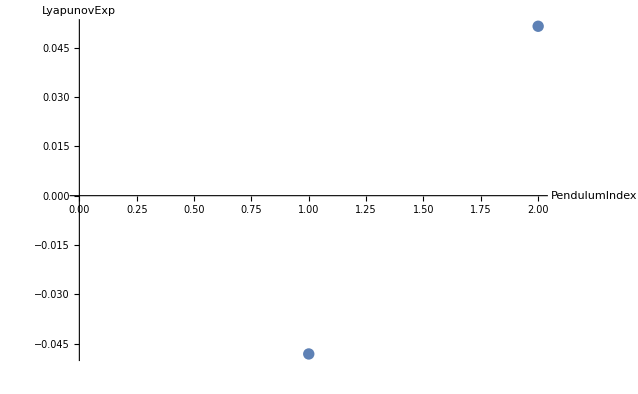

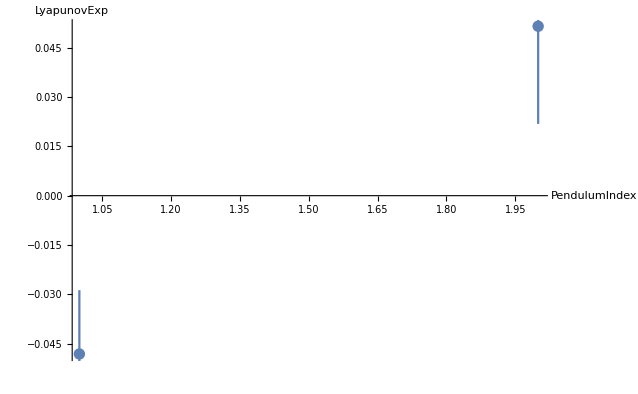

```mathematica
lambdaavg=Flatten[Table[Sum[lambdas[[j,i]],{j,1,runs}]/tmax,{i,1,n}]]
ListPlot[Flatten[lambdaavg],AxesLabel->{PendulumIndex,LyapunovExp}] (* plots averages lambdas *)
lambdasrearrange=Table[lambdas[[j,i]],{j,1,runs},{i,1,n}];
lambdaserr=Table[{lambdaavg[[i]],StandardDeviation[Flatten[lambdasrearrange[[i]]/deltat]]/Sqrt[runs]},{i,1,n}]; (* table of {lambdai_i,errlambda_i} to plot with errors *)
Needs["ErrorBarPlots`"]
ErrorListPlot[lambdaserr,AxesLabel->{PendulumIndex,LyapunovExp}]
```

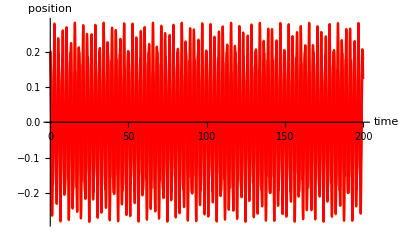

```mathematica
plots=Table[Plot[Evaluate[Table[phi[i][t]/.posruns[[j]]/.t->(t-deltat(j-1)),{i,1,n}]],{t,deltat(j-1),deltat*j},AxesLabel->{time,position},ImageSize->Full],{j,1,runs}];

Show[plots,
Plot[Evaluate[Table[phi[i][t]/.posrun0,{i,1,n}]],{t,0,tmax},PlotStyle->Red],
PlotRange->All
]
```